# InsertionMapping Package Usage

This package has been developed for analyzing a peptide insertion screen (Buermann et al., 2017, Mol Cell). It contains functions for mapping deep-sequencing reads with a specific insert to a target sequence, and for statistical analysis of the experiment.

This notebook demonstrates the usage of the mapping functionality.

Make sure the package is in the folder opened by:

```mathematica
SystemOpen[FileNameJoin[{$UserBaseDirectory,"Applications"}]]
```

Let's load the package:

```mathematica
<<InsertionMapping`
```

```mathematica
?"InsertionMapping`*"
```

Let’s define a root folder function:

```mathematica
root=FileNameJoin[{$UserBaseDirectory,"Applications","InsertionMapping","Usage",##}]&;
```

Let’s define the parental plasmid sequence and the insert sequence:

```mathematica
targetSeq=Import[root@"pSG1134.txt","String"];
ins="ctgtctgcctcctccgcctcccggtccagacag";
```

Now we load the read sequences from the deep-sequencing experiment (this is only 10^5 reads in this example):

```mathematica
reads=importFastq[root@"seqData.fastq"]⟦All,"Sequence"⟧;
```

Now we use the insertionMapper function to map reads containing the insert to the target:

```mathematica
mapping=insertionMapper[targetSeq,ins,reads];
```

Let’s filter out mapped reads and get their positions:

```mathematica
basePos=
MapAt[
DeleteCases[#,{0,0}]⟦1,1⟧&,
mapping//Select[#Direction=!="NA"&]
,{All,"Mappings"}
];
```

Let’s plot the result:

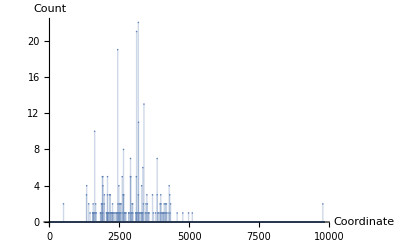

```mathematica
ListPlot[
BinCounts[Values@basePos⟦All,"Mappings"⟧,{1,StringLength@targetSeq+1,1}]
,Filling->Axis
,PlotRange->All
,AxesLabel->{"Coordinate","Count"}
]
```

The coding sequence (CDS) its coordinates are:

```mathematica
cdsCoords={1007,4564};
cds=StringTake[targetSeq,cdsCoords];
```

Now we filter out the reads mapping to the CDS, find the insert positions on amino acid level, and plot the result:

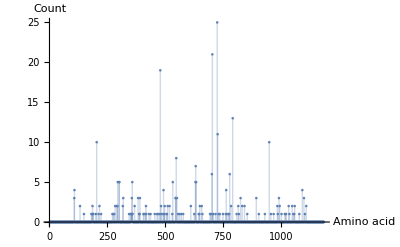

```mathematica
aaPos=
basePos//Select[cdsCoords⟦1⟧≤#Mappings≤cdsCoords⟦2⟧&]//Map[
findUpstreamCodon[cds,ins,#Mappings-cdsCoords⟦1⟧+1,#Direction]&
];

ListPlot[
BinCounts[Values@aaPos,{1,StringLength@translateCDS@cds+1,1}]
,Filling->Axis
,PlotRange->All
,AxesLabel->{"Amino acid","Count"}
]
```